Remember to add 4.4 in class!

# HW Zero

### 3.1

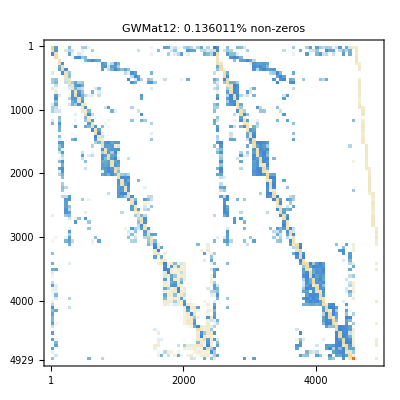

```mathematica
A=Import["https://math.nist.gov/pub/MatrixMarket2/Harwell-Boeing/gemat/gemat12.mtx.gz"];
MatrixPlot[A,PlotLabel->StringForm["GWMat12: ``% non-zeros",100*A["Density"]]]
```

### 3.3

```mathematica
Eigenvalues[A,{3}]
```

{5.2894-1.20544 ⅈ}

### 3.2 and 3.4

```mathematica
{m,n}=Dimensions[A];
b=SparseArray[1->1.0,m];
LinearSolve[A,b][[3]]
```

1.11486

### 3.5 and 3.6

{0.820325,Null}

SingularValueList::arh: Because finding 4929 out of the 4929 singular values and/or singular vectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer singular values and/or singular vectors would be sufficient, consider restricting this number using the second argument to SingularValueList.

{50.0107,Null}

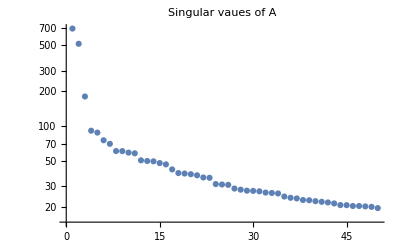

```mathematica
AbsoluteTiming[σ=SingularValueList[A,50];]
AbsoluteTiming[SingularValueList[A];]
ListLogPlot[σ,PlotLabel->"Singular vaues of A"]
```

Wow it took just under a second to compute the first 50 and and roughly 50 second to compute them all!

### 4.1

```mathematica
B=RandomReal[{-1,1},{20,20}]; A=B.Bᵀ;
{U,S,V}=SingularValueDecomposition[A];
MatrixPlot[S,
PlotLegends->Automatic,PlotLabel->StringForm["||A-U.S.Vᵀ||/||A||=``", Norm[A-U.S.Vᵀ]/Norm[A]]]
```

-Graphics-

### 4.2

```mathematica
B=RandomReal[{-1,1},{20,20}]; A=B.Bᵀ;
{Q,R}=QRDecomposition[A]; Q=Qᵀ;
MatrixPlot[R,
PlotLegends->Automatic,PlotLabel->StringForm["||A-Q.R||/||A||=``", Norm[A-Q.R]/Norm[A]]]
```

-Graphics-

### 4.3

```mathematica
B=RandomReal[{-1,1},{20,20}]; A=B.Bᵀ;
U=CholeskyDecomposition[A]; L=Uᵀ;
MatrixPlot[S,
PlotLegends->Automatic,PlotLabel->StringForm["||A-L.Lᵀ||/||A||=``", Norm[A-L.Lᵀ]/Norm[A]]]
```

-Graphics-